# SIS model figure

We are going to show how the two movement models differ from one another, using output Prevalences as a function of β_i

The most significant thing to show is that different parameter regimes - comparing infectious periods with travel periods - drive whether the models agree or not.
When infectious periods are about the same as periods at home (as in malaria), we get disagreement between the models.  When infectious periods are very fast compared to the periods at home (as in flu) we get closer agreement.

## SIS Model Definition

```mathematica
(* The TaR movement model *)
movtar ={0 == - ϕ1 n11 + τ12 n12,
0 == - ϕ2 n22+ τ21  n21,
(* Normalize to the residence populations *)
n11 + n12 == n1,
n22 + n21 == n2
};
(* The transmission model *)
sistar ={(* On-diagonal terms *)
0 == β1(i11 + i21)/(n11+n21)(n11 - i11) - γ i11 - ϕ1 i11 + τ12 i12,
0 == β2(i22 + i12)/(n22 + n12)(n22 - i22) - γ i22 - ϕ2 i22 + τ21 i21,
(* Off-diagonal terms *)
0 == β2(i22 + i12)/(n22 + n12)(n12 - i12) - γ i12 + ϕ1 i11 - τ12 i12,
0 == β1 (i11 + i21)/(n11 + n21)(n21 - i21) - γ i21 + ϕ2 i22 - τ21 i21
};
```

```mathematica
(* The Flux movement model *)
movflux ={0 == - f1 n1 + f2 n2,
(* Normalize to the total population *)
n ==n1+n2
};
(* The transmission model *)
sisflux ={
0 == β1  i1/n1(n1 - i1) - γ i1 - f1 i1 + f2 i2,
0 == β2  i2/n2(n2 - i2) - γ i2 -f2 i2+ f1 i1
};
```

```mathematica
(* Matching Flux Volumes *)
mtar ={m12-> (τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2,m21->(τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2};
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar
```

{f1→((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n1,f2→((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n2}

## Figure Generation - symmetric travel

```mathematica
(* Define parameters *)
tarpars= {ϕ1->.5/100, τ12 ->40/1,ϕ2->.5/100,τ21 ->40/1};
poppars={n1->500.,n2->500.};
sispars={γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->1000,{n1,n2}]];
```

The best way to describe this parameter regime is one where people from location 1 travel more frequently to location 2, but that all visits lasts about the same amount of time.

```mathematica
movTarSols
movFluxSols
```

{n11→499.938,n12→0.0624922,n22→499.938,n21→0.0624922}

{n1→500.,n2→500.}

### Holding β2 = 5

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->2.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->2.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

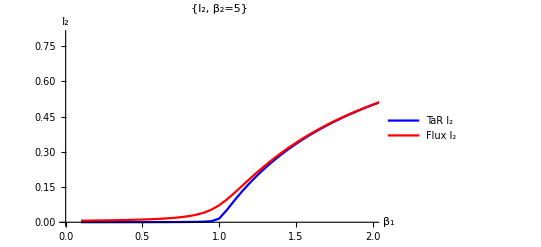

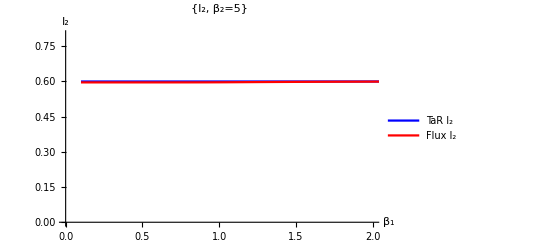

```mathematica
(* Making a Figure: *)
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]]
(*,tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=5"},
PlotRange->{{0,2},{0,.8}}]

ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=5"},
PlotRange->{{0,2},{0,.8}}]
```

### Holding β2 = .5 < γ = 1

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

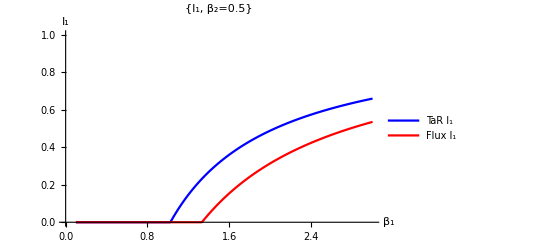

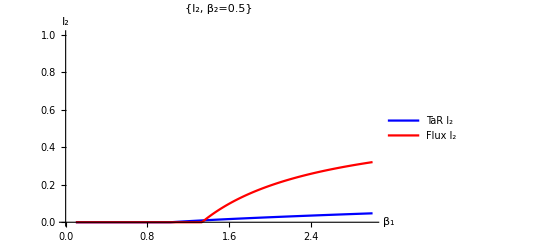

```mathematica
(* Making a Figure: *)
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]](*,
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_1"},
PlotLabel->{"I_1, β_2=0.5"},
PlotRange->{{0,3},{0,1}}]
ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=0.5"},
PlotRange->{{0,3},{0,1}}]
```

## Figure Generation - asymmetric travel

```mathematica
(* Define parameters *)
tarpars= {ϕ1->0, τ12 ->40,ϕ2->0.5,τ21 ->40};
poppars={n1->500.,n2->500.};
sispars={γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->1000,{n1,n2}]];
```

The best way to describe this parameter regime is one where people from location 1 travel more frequently to location 2, but that all visits lasts about the same amount of time.

```mathematica
movTarSols
movFluxSols
```

{n11→500.,n12→0.,n22→493.827,n21→6.17284}

{n1→500.,n2→500.}

### Holding β2 = 5

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

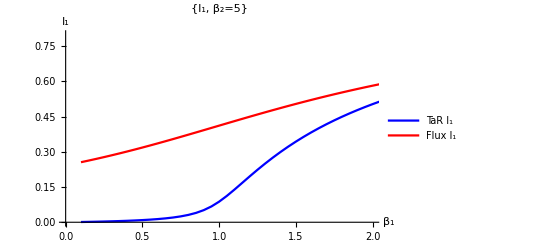

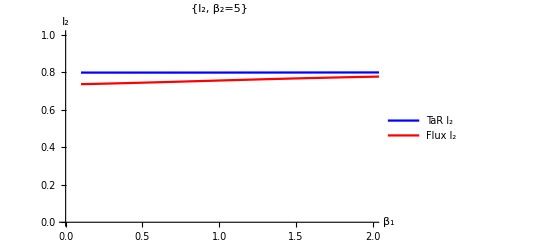

```mathematica
(* Making a Figure: *)
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]](*,
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_1"},
PlotLabel->{"I_1, β_2=5"},
PlotRange->{{0,2},{0,.8}}]
ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=5"},
PlotRange->{{0,2},{0,1}}]
```

### Holding β2 = .5 < γ = 1

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

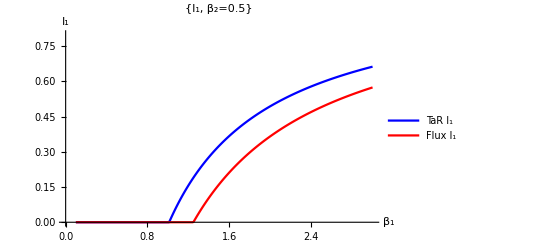

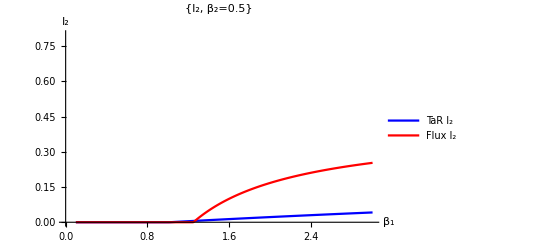

```mathematica
(* Making a Figure: *)
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]](*,
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_1"},
PlotLabel->{"I_1, β_2=0.5"},
PlotRange->{{0,3},{0,.8}}]
ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=0.5"},
PlotRange->{{0,3},{0,.8}}]
```

## Figure Generation - fast travel

Pick travel times that are comparable to the infectious period; travel frequency comparable to the rate of recovery

```mathematica
(* Define parameters *)
tarpars= {ϕ1->.5, τ12 ->40,ϕ2->.5,τ21 ->40};
poppars={n1->500.,n2->500.};
sispars={γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->1000,{n1,n2}]];
```

The best way to describe this parameter regime is one where people from location 1 travel more frequently to location 2, but that all visits lasts about the same amount of time.

```mathematica
movTarSols
movFluxSols
```

{n11→493.827,n12→6.17284,n22→493.827,n21→6.17284}

{n1→500.,n2→500.}

### Holding β2 = 2.5

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->2.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,0,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->2.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,0,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

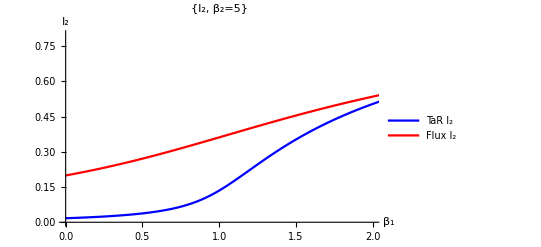

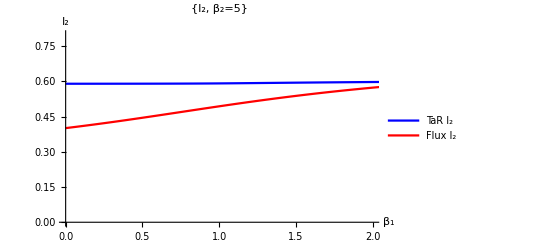

```mathematica
(* Making a Figure: *)
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]]
(*,tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=5"},
PlotRange->{{0,2},{0,.8}}]

ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=5"},
PlotRange->{{0,2},{0,.8}}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/Fast_high.csv",Transpose[{tarPRSlices[[;;,1]],tarPRSlices[[;;,2]],fluxPRSlices[[;;,2]],tarPRSlices[[;;,3]],fluxPRSlices[[;;,3]]}]]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/Fast_high.csv

```mathematica
Dimensions[tarPRSlices]
```

{291,3}

### Holding β2 = .5 < γ = 1

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,0,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,0,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

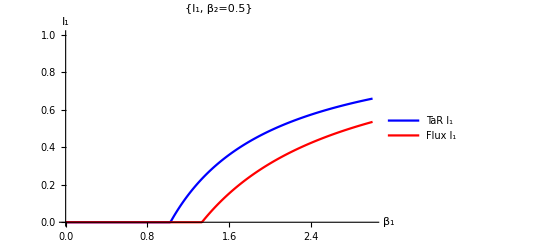

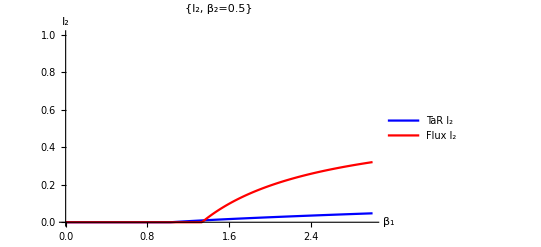

```mathematica
(* Making a Figure: *)
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]](*,
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_1"},
PlotLabel->{"I_1, β_2=0.5"},
PlotRange->{{0,3},{0,1}}]
ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=0.5"},
PlotRange->{{0,3},{0,1}}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/Fast_low.csv",Transpose[{tarPRSlices[[;;,1]],tarPRSlices[[;;,2]],fluxPRSlices[[;;,2]],tarPRSlices[[;;,3]],fluxPRSlices[[;;,3]]}]]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/Fast_low.csv

## Figure Generation - slow travel

Pick travel times that are much longer than the infectious period; travel frequency is slower than the rate of recovery

```mathematica
(* Define parameters *)
tarpars= {ϕ1->.5/100, τ12 ->40/100,ϕ2->.5/100,τ21 ->40/100};
poppars={n1->500.,n2->500.};
sispars={γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->1000,{n1,n2}]];
```

The best way to describe this parameter regime is one where people from location 1 travel more frequently to location 2, but that all visits lasts about the same amount of time.

```mathematica
movTarSols
movFluxSols
```

{n11→493.827,n12→6.17284,n22→493.827,n21→6.17284}

{n1→500.,n2→500.}

### Holding β2 = 5

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->2.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,0,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->2.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,0,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

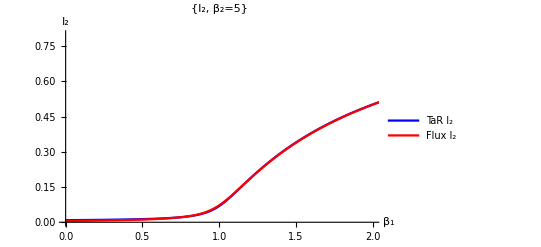

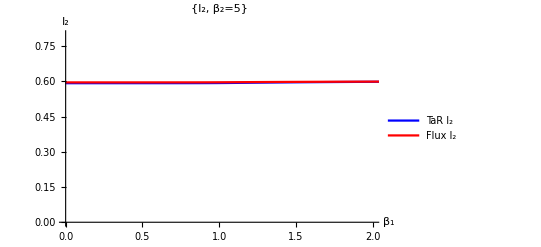

```mathematica
(* Making a Figure: *)
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]]
(*,tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=5"},
PlotRange->{{0,2},{0,.8}}]

ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=5"},
PlotRange->{{0,2},{0,.8}}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/Slow_high.csv",Transpose[{tarPRSlices[[;;,1]],tarPRSlices[[;;,2]],fluxPRSlices[[;;,2]],tarPRSlices[[;;,3]],fluxPRSlices[[;;,3]]}]]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/Slow_high.csv

### Holding β2 = .5 < γ = 1

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,0,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,0,3,.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

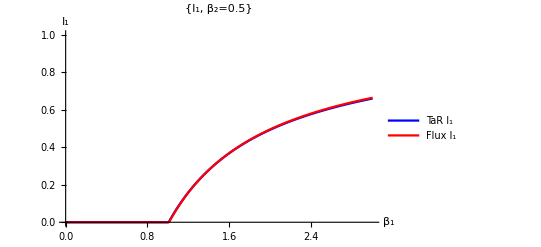

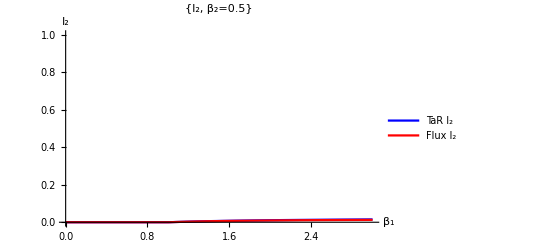

```mathematica
(* Making a Figure: *)
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]](*,
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_1"},
PlotLabel->{"I_1, β_2=0.5"},
PlotRange->{{0,3},{0,1}}]
ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=0.5"},
PlotRange->{{0,3},{0,1}}]
```

```mathematica
Export["/Users/dtcitron/Documents/Publications/TarFlux/Data/Slow_low.csv",Transpose[{tarPRSlices[[;;,1]],tarPRSlices[[;;,2]],fluxPRSlices[[;;,2]],tarPRSlices[[;;,3]],fluxPRSlices[[;;,3]]}]]
```

/Users/dtcitron/Documents/Publications/TarFlux/Data/Slow_low.csv

# SIR model figure

```mathematica
(* This is the TaR model *)
TarVars = {s11[t],s12[t],s22[t],s21[t],i11[t],i12[t],i22[t],i21[t],r11[t],r12[t],r22[t],r21[t]};
sirTar ={
D[s11[t],t]== -β1(i11[t] + i21[t])/(s11[t]+i11[t]+r11[t]+s21[t]+i21[t]+r21[t])s11[t]- ϕ1 s11[t] + τ12 s12[t],
D[s12[t],t]== -β2(i22[t] + i12[t])/(s22[t]+i22[t]+r22[t]+s12[t]+i12[t]+r12[t])s12[t]+ ϕ1 s11[t] - τ12 s12[t],
D[s22[t],t]== -β2(i22[t] + i12[t])/(s22[t]+i22[t]+r22[t]+s12[t]+i12[t]+r12[t])s22[t]-ϕ2 s22[t] + τ21 s21[t],
D[s21[t],t]==-β1(i11[t] + i21[t])/(s11[t]+i11[t]+r11[t]+s21[t]+i21[t]+r21[t])s21[t]+ ϕ2 s22[t] - τ21 s21[t],
D[i11[t],t]== β1(i11[t] + i21[t])/(s11[t]+i11[t]+r11[t]+s21[t]+i21[t]+r21[t])s11[t] - γ i11[t] - ϕ1 i11[t] + τ12 i12[t],
D[i12[t],t]== β2(i22[t] + i12[t])/(s22[t]+i22[t]+r22[t]+s12[t]+i12[t]+r12[t])s12[t]- γ i12[t] + ϕ1 i11[t] - τ12 i12[t],
D[i22[t],t]== β2(i22[t] + i12[t])/(s22[t]+i22[t]+r22[t]+s12[t]+i12[t]+r12[t])s22[t] - γ i22[t] - ϕ2 i22[t] + τ21 i21[t],
D[i21[t],t]== β1 (i11[t] + i21[t])/(s11[t]+i11[t]+r11[t]+s21[t]+i21[t]+r21[t])s21[t] - γ i21[t] + ϕ2 i22[t] - τ21 i21[t],
D[r11[t],t]==γ i11[t]- ϕ1 r11[t] + τ12 r12[t],
D[r12[t],t]==γ i12[t]+ ϕ1 r11[t] - τ12 r12[t],
D[r22[t],t]==γ i22[t] - ϕ2 r22[t]+ τ21 r21[t],
D[r21[t],t]==γ i21[t] + ϕ2 r22[t]- τ21 r21[t]
};
```

```mathematica
(* And the flux model *) 
stvec = {S1[t],S2[t]};
itvec = {I1[t],I2[t]};
rtvec = {R1[t],R2[t]};
nvec = {n1,n2};
βvec = {β1,β2};
fij = {{0,f12},{f21,0}};
sirFlux = Table[Flatten[{D[stvec,t],D[itvec,t],D[rtvec,t]}][[j]]==Flatten[{-βvec itvec stvec/nvec + Transpose[fij].stvec - fij.{1,1}*stvec,
+ βvec itvec stvec/nvec + Transpose[fij].itvec - fij.{1,1}*itvec - γ itvec,
γ itvec+ Transpose[fij].rtvec - fij.{1,1}*rtvec}][[j]],{j,1,6}];
(*sirFlux/.sirpars/.poppars/.fluxpars//MatrixForm*)
```

We are going to show how the two models differ from one another, using Next Generation Matrix calculations of R0 as a function of β_i

NOTE: it is weirdly hard to find a regime where either the NGM or other quantitative ways of showing the impact of the SIR epidemic on the connected populations is very different.  For now we will leave these out.

```mathematica
(* Define parameters *)
tarpars= {ϕ1->1, τ12 ->40,ϕ2->1,τ21 ->40};
poppars={n1->500.,n2->500.};
sirpars={γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->1000,{n1,n2}]];
```

```mathematica
movTarSols
movFluxSols
```

{n11→487.805,n12→12.1951,n22→487.805,n21→12.1951}

{n1→500.,n2→500.}

```mathematica
(* TaR: next generation matrix *)
T={{(n11 β1)/(n11+n21),0,0,(n11 β1)/(n11+n21)},{0,(n12 β2)/(n22+n12),(n12 β2)/(n22+n12),0},{0,(n22 β2)/(n22+n12),(n22 β2)/(n22+n12),0},{(n21 β1)/(n11+n21),0,0,(n21 β1)/(n11+n21)}};
Σ={{-γ-ϕ1,τ12,0,0},{ϕ1,-γ-τ12,0,0},{0,0,-γ-ϕ2,τ21},{0,0,ϕ2,-γ-τ21}};
tarSol = Sort[Eigenvalues[-T.Inverse[Σ]/.movTarSols/.tarpars/.sirpars],Greater]
```

{0,Root[-1.0842×10^-19 β1^2 β2-1.25924×10^-22 β1 β2^2+(2.1684×10^-19 β1^2+0.907085 β1 β2+2.1684×10^-19 β2^2) #1+(-0.953542 β1-0.953542 β2) #1^2+1. #1^3&,1],Root[-1.0842×10^-19 β1^2 β2-1.25924×10^-22 β1 β2^2+(2.1684×10^-19 β1^2+0.907085 β1 β2+2.1684×10^-19 β2^2) #1+(-0.953542 β1-0.953542 β2) #1^2+1. #1^3&,2],Root[-1.0842×10^-19 β1^2 β2-1.25924×10^-22 β1 β2^2+(2.1684×10^-19 β1^2+0.907085 β1 β2+2.1684×10^-19 β2^2) #1+(-0.953542 β1-0.953542 β2) #1^2+1. #1^3&,3]}

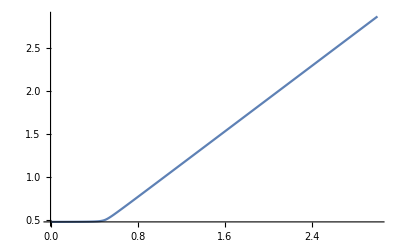

```mathematica
Plot[tarSol[[4]]/.β2->.5,{β1,0,3}]
```

```mathematica
(* Flux: Next Generation matrix *)
T = {{β1,0},{0,β2}};
Σ={{-(γ+f1),f2},{f1,-(γ+f2)}};
fluSol = Sort[Eigenvalues[-T.Inverse[Σ]/.fluxpars/.sirpars],Greater]
```

{0.5 (0.60199 β1+0.60199 β2-√(0.362392 β1^2-0.0911364 β1 β2+0.362392 β2^2)),0.5 (0.60199 β1+0.60199 β2+√(0.362392 β1^2-0.0911364 β1 β2+0.362392 β2^2))}

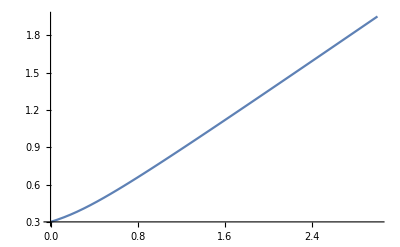

```mathematica
Plot[Max[fluSol/.β2->.5],{β1,0,3}]
```

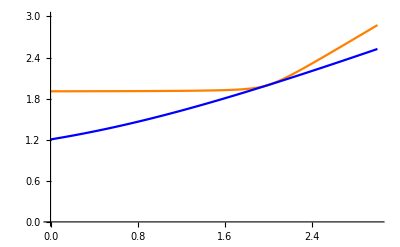

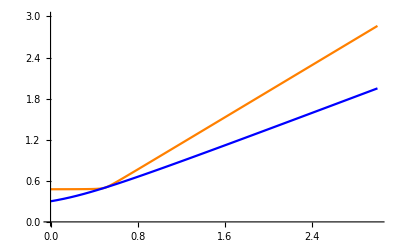

```mathematica
Plot[{tarSol[[4]]/.β2->2,Max[fluSol/.β2->2]},{β1,0,3},PlotStyle->{Orange,Blue},PlotRange->{0,3}]
Plot[{tarSol[[4]]/.β2->.5,Max[fluSol/.β2->.5]},{β1,0,3},PlotStyle->{Orange,Blue},PlotRange->{0,3}]
```

For this next section, we can see how the size of the epidemic changes based on the parameters

```mathematica
(* Defining parameters *)
poppars={n1->500.,n2->500.};
(* Aligning Movement parameters *)
tarpars= {ϕ1->.5, τ12 ->40,ϕ2->.5,τ21 ->40};(*{ϕ1->1/200., τ12 ->1/15.,ϕ2->1/200.,τ21 ->1/15.}*);
movtar ={0 == - ϕ1 n11 + τ12 n12,
0 == - ϕ2 n22+ τ21  n21,
(* Normalize to the residence populations *)
n11 + n12 == n1,
n22 + n21 == n2
};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
mtar ={m12-> (τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2,m21->(τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2};
fluxpars ={f12->(m12/n1),f21->(m21/n2)}/.mtar/.tarpars/.poppars;
```

```mathematica
TarVars = {
s11[t],s12[t],s22[t],s21[t].10,
i11[t],i12[t],i22[t],i21[t],
r11[t],r12[t],r22[t],r21[t]};
rTar = Table[qTar = NDSolve[Flatten[{sirTar,
{s11[0]==n1-1,s12[0]==0,s22[0]==n2-1,s21[0]==0,
i11[0]==1,i12[0]==0,i22[0]==1,i21[0]==0,
r11[0]==0,r12[0]==0,r22[0]==0,r21[0]==0}}]/.{γ->1.,β2->2,β1->i}/.poppars/.tarpars/.fluxpars,
TarVars,
{t,0,10000}];
{i,(r11[t]+r12[t]+r22[t]+r21[t])/(n1+n2)/.qTar[[1]]/.t->10000/.poppars},{i,0,5,.05}];
```

```mathematica
rFlux = Table[qFlux=NDSolve[Flatten[{sirFlux,
{S1[0]==n1-1,S2[0]==n2-1,I1[0]==1,I2[0]==1,R1[0]==0,R2[0]==0}}]/.{γ->1.,β2->2,β1->i}/.poppars/.tarpars/.fluxpars,
Flatten[{stvec,itvec,rtvec}],
{t,0,1000000}];
{i,(R1[t]+R2[t])/(n1+n2)/.qFlux[[1]]/.t->10000/.poppars},{i,0,5,.05}];
```

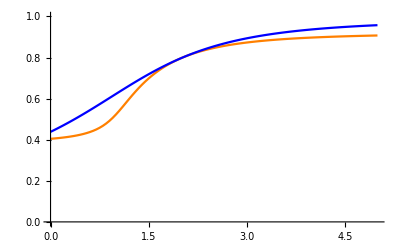

```mathematica
ListLinePlot[{rTar,rFlux},PlotStyle->{Orange,Blue},PlotRange->{{0,5},{0,1}}]
```

```mathematica
rTar = Table[qTar = NDSolve[Flatten[{sirTar,
{s11[0]==n1-1,s12[0]==0,s22[0]==n2-1,s21[0]==0,
i11[0]==1,i12[0]==0,i22[0]==1,i21[0]==0,
r11[0]==0,r12[0]==0,r22[0]==0,r21[0]==0}}]/.{γ->1.,β2->.5,β1->i}/.poppars/.tarpars/.fluxpars,
TarVars,
{t,0,10000}];
{i,(r11[t]+r12[t]+r22[t]+r21[t])/(n1+n2)/.qTar[[1]]/.t->10000/.poppars},{i,0,5,.05}];
```

```mathematica
rFlux = Table[qFlux=NDSolve[Flatten[{sirFlux,
{S1[0]==n1-1,S2[0]==n2-1,I1[0]==1,I2[0]==1,R1[0]==0,R2[0]==0}}]/.{γ->1.,β2->.5,β1->i}/.poppars/.tarpars/.fluxpars,
Flatten[{stvec,itvec,rtvec}],
{t,0,10000}];
{i,(R1[t]+R2[t])/(n1+n2)/.qFlux[[1]]/.t->10000/.poppars},{i,0,5,.05}];
```

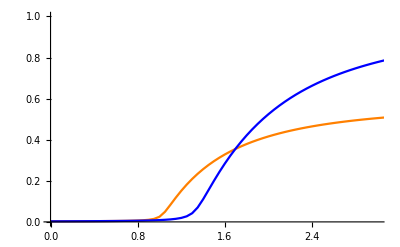

```mathematica
ListLinePlot[{rTar,rFlux},PlotStyle->{Orange,Blue},PlotRange->{{0,3},{0,1}}]
```

```mathematica
rTar = Table[qTar = NDSolve[Flatten[{sirTar,
{s11[0]==n1-1,s12[0]==0,s22[0]==n2-1,s21[0]==0,
i11[0]==1,i12[0]==0,i22[0]==1,i21[0]==0,
r11[0]==0,r12[0]==0,r22[0]==0,r21[0]==0}}]/.{γ->1.,β2->1.5,β1->i}/.poppars/.tarpars/.fluxpars,
TarVars,
{t,0,10000}];
{i,(r11[t]+r12[t]+r22[t]+r21[t])/(n1+n2)/.qTar[[1]]/.t->10000/.poppars},{i,0,5,.05}];
```

```mathematica
rFlux = Table[qFlux=NDSolve[Flatten[{sirFlux,
{S1[0]==n1-1,S2[0]==n2-1,I1[0]==1,I2[0]==1,R1[0]==0,R2[0]==0}}]/.{γ->1.,β2->1.5,β1->i}/.poppars/.tarpars/.fluxpars,
Flatten[{stvec,itvec,rtvec}],
{t,0,10000}];
{i,(R1[t]+R2[t])/(n1+n2)/.qFlux[[1]]/.t->10000/.poppars},{i,0,5,.05}];
```

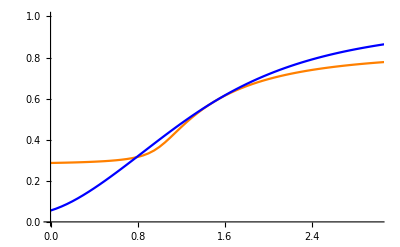

```mathematica
ListLinePlot[{rTar,rFlux},PlotStyle->{Orange,Blue},PlotRange->{{0,3},{0,1}}]
```